```mathematica
system = BinaryReadList["C:\\Users\\jacks\\Documents\\GitHub\\Qnibble\\Scripts\\mySystem.dat",{"Complex128"}];
system = ArrayReshape[system,{2^4,2^4}];

env = BinaryReadList["C:\\Users\\jacks\\Documents\\GitHub\\Qnibble\\Scripts\\myEnvironment.dat",{"Complex128"}];
env = ArrayReshape[env,{2^4,2^4}];

tot = BinaryReadList["C:\\Users\\jacks\\Documents\\GitHub\\Qnibble\\Scripts\\myTotal.dat",{"Complex128"}];
tot = ArrayReshape[tot,{2^8,2^8}];
```

```mathematica
Entr[S_]:=Re[-Tr[Dot[S,MatrixLog[S]]]]
```

```mathematica
Entr[system]+Entr[env]
```

3.04816

```mathematica
Entr[tot]
```

4.13666

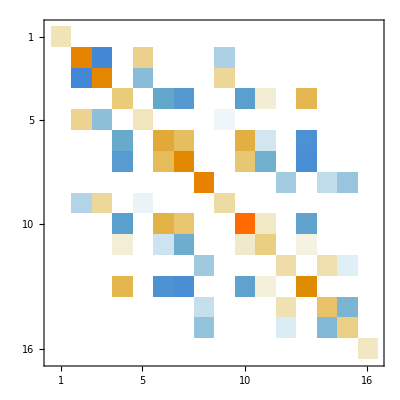

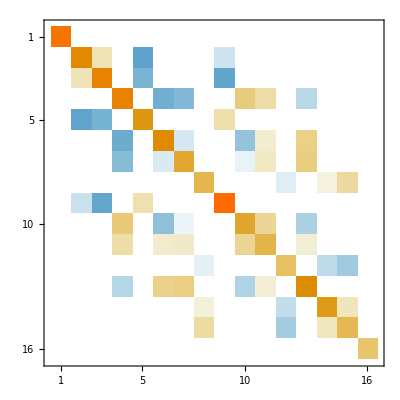

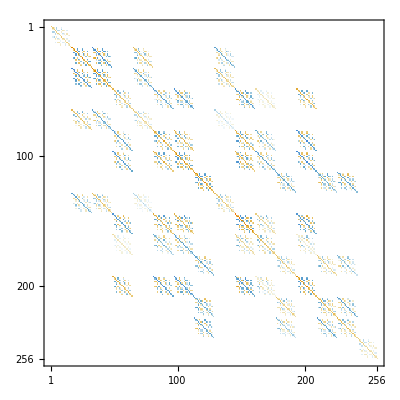

```mathematica
MatrixPlot[system]
MatrixPlot[env]
MatrixPlot[tot]
```